This is a notebook created on October 2022 to implement the Kohn correction to the phase shift, the Empirical Interpolation Method, and the boundary conditions using Phi_0 (see Eq. (2) in https://arxiv.org/pdf/2203.05284v2.pdf) for the Bayesian Analysis for Nuclear Dynamics collaboration on the implementation of Reduced Basis Methods nuclear scattering. We use the Minnesota potential for the example. The boundary conditions are used at the origin instead of the often used approach in the asymptotics. 

-Graphics-;

```mathematica
Eqs=-D2.Wf+(l*(l+1)/x^2+Vpot-1)*Wf;

-Graphics-    ;
```

This is the scaled equation we are solving for. Notice that , since the usual variable r is re-scaled as s=r*p, then the only thing that depends on the energy is the effective potential \tilde U, allowing us to mix solutions for different energies and emulate across them. Not only that, the only information of the particular nucleus under consideration is also on \tilde U, both through its parameters and through the reduced mass \mu, which means we can emulate across nuclei as well.

## Defining the grid space and global variables

```mathematica
dx=0.05;
XMin=dx;
XMax=20;
xList=Range[XMin,XMax,dx];
```

```mathematica
len=Length[xList];
```

```mathematica
epsilon=0.01;
```

```mathematica
D2Mat=SparseArray[{Band[{1,1}]->-30,Band[{2,1}]->16,Band[{1,2}]->16,Band[{1,3}]->-1,Band[{3,1}]->-1},{len,len}]/(12*dx^2);
D2Mat[[1]][[1]]=-2/(dx^2);
D2Mat[[1]][[2]]=1/(dx^2);
D2Mat[[1]][[3]]=0;
```

```mathematica
D1Mat=SparseArray[{Band[{2,1}]->-8,Band[{1,2}]->8,Band[{1,3}]->-1,Band[{3,1}]->1},{len,len}]/(12*dx);
```

```mathematica
V[r_,V0R_,V0S_,EE_]=(V0R*Exp[-1.487*(r/(Sqrt[EE]*MuFactor))^2]+V0S*Exp[-0.465*(r/(Sqrt[EE]*MuFactor))^2])1/EE
```

(ⅇ^(-(1.487 r^2)/(EE MuFactor^2)) V0R+ⅇ^(-(0.465 r^2)/(EE MuFactor^2)) V0S)/EE

```mathematica
MuFactor=Sqrt[2*1/2*939.565/(197.326)^2]
```

0.155338

```mathematica
hbarc=197.326;
```

```mathematica
(*mu=hbarc^2/41.47105/2;*)
```

```mathematica
mNeu=939.565/197.326;
(*mNeu=hbarc^2/41.47105;*)
(*mu=(mNeu*1*mNeu*1)/(mNeu*(1))*)
```

## Solving the system with a numerical approach (we are keeping the non linear parameters fixed for this part)

```mathematica
EqSolver[V0R_,V0S_,EE_,l_]:=PHI/.NDSolve[{-PHI''[XX]+(l*(l+1)/XX^2+V[XX,V0R,V0S,EE]-1)*PHI[XX]==0,PHI[epsilon]==epsilon^(l+1)/((2*l+1)!!),PHI'[epsilon]==(l+1)*epsilon^(l)/((2*l+1)!!)},PHI,{XX,epsilon,3*XMax},MaxStepSize->0.001][[1]][[1]](*Added the factor of 3 to XMax because otherwise with the change of variables the function had to extrapolate*)
```

```mathematica
SolutionExact=EqSolver[200.,−91.85,50,0]
```

InterpolatingFunction[{{0.01, 60.}}, <>]

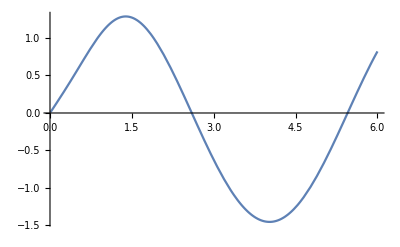

```mathematica
Plot[SolutionExact[x*Sqrt[50]*MuFactor],{x,0.01,6}]
```

```mathematica
-Graphics-;
```

```mathematica
F[rho_,LL_]=rho*SphericalBesselJ[LL,rho]
```

rho SphericalBesselJ[LL,rho]

```mathematica
G[rho_,LL_]=-rho*SphericalBesselY[LL,rho]
```

-rho SphericalBesselY[LL,rho]

```mathematica
HPlus[rho_,LL_]=G[rho,LL]+I*F[rho,LL]
```

ⅈ rho SphericalBesselJ[LL,rho]-rho SphericalBesselY[LL,rho]

```mathematica
HMinus[rho_,LL_]=G[rho,LL]-I*F[rho,LL]
```

-ⅈ rho SphericalBesselJ[LL,rho]-rho SphericalBesselY[LL,rho]

```mathematica
HMinusPrime[rho_,LL_]=D[HMinus[rho,LL],rho];
```

```mathematica
HPlusPrime[rho_,LL_]=D[HPlus[rho,LL],rho];
```

```mathematica
FL[rho_,LL_]=(HPlus[rho,LL]-HMinus[rho,LL])/(2*I);
```

```mathematica
X0=19;
(*n0 is the value in the list that corresponds to X0, very important to keep for Galerkin stuff later!*)
n0=Round[X0/dx]
```

380

```mathematica
xList[[n0]]
```

19.

```mathematica
If[xList[[n0]]!=X0,
Print["AAAAAAAAAAAAAAAAAAAH PROBLEMS!!"];
EmitSound[Sound[SoundNote[]]];
Speak["Be careful, your grid end point is not correct!"]

]
```

```mathematica
NormSolver[Yval_,YvalP_,LL_]:=Module[{RL},

RL=1/X0*(Yval/YvalP);

Log[(HMinus[X0,LL]-X0*RL*HMinusPrime[X0,LL])/(HPlus[X0,LL]-X0*RL*HPlusPrime[X0,LL])]/(2*I)

]
```

```mathematica
TruePhiSolver[V0R_,V0S_,EE_,l_]:=Module[{Func,DelDel},

Func=EqSolver[V0R,V0S,EE,l];

DelDel=NormSolver[Func[X0],Func'[X0],l];
{DelDel,Table[Func[xList[[XXi]]],{XXi,1,Length[xList]}]}



]
```

```mathematica
EnergyGrid=Join[Range[0.1,2,0.4],Range[3,10,4],Range[15,100,10],Range[120,150,20]]
```

{0.1,0.5,0.9,1.3,1.7,3,7,15,25,35,45,55,65,75,85,95,120,140}

```mathematica
(*EnergyGrid=Range[5,9,0.2]*)
```

```mathematica
Params0={200.,−91.85};
```

```mathematica
MaxL=0;
```

```mathematica
LValuesList=Table[{},{i,1,MaxL+1}]
```

{{}}

```mathematica
For[pInd=1,pInd<=Length[EnergyGrid],pInd++,

For[LInd=1,LInd<=MaxL+1,LInd++,

AppendTo[LValuesList[[LInd]],180/Pi*TruePhiSolver[Params0[[1]],Params0[[2]],EnergyGrid[[pInd]],LInd-1][[1]]]



]




]
```

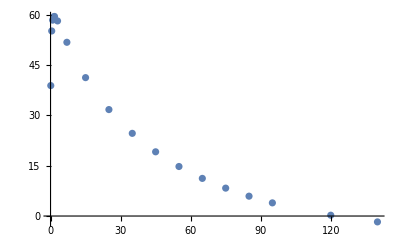

```mathematica
ListPlot[Transpose[{EnergyGrid,LValuesList[[1]]}]]
```

```mathematica
-Graphics-;
```

## RBMs!

## First step: Create a basis and “trial” wave function

```mathematica
E0=50;
```

```mathematica
TruePhiSolverParamList[ParamList_,EE_,l_]:=TruePhiSolver[ParamList[[1]],ParamList[[2]],EE,l]
```

```mathematica
(*ParamTraining={{0.,−291.85},{100.,8.15},{300.,−191.85}, {300.,8.15}};*)
```

```mathematica
TrainingPoints={{119.51219512195122,-14.634146341463415},{139.02439024390245,-4.878048780487805},{158.53658536585365,-48.78048780487805},{178.0487804878049,-117.07317073170732},{197.5609756097561,-131.70731707317074},{217.0731707317073,-126.82926829268293},{236.58536585365854,-82.92682926829268},{256.0975609756098,-175.609756097561},{275.609756097561,-19.51219512195122},{295.1219512195122,-170.73170731707316}};
```

```mathematica
SolutionsCont=Table[TruePhiSolverParamList[TrainingPoints[[i]],E0,0][[2]],{i,1,Length[TrainingPoints]}];
```

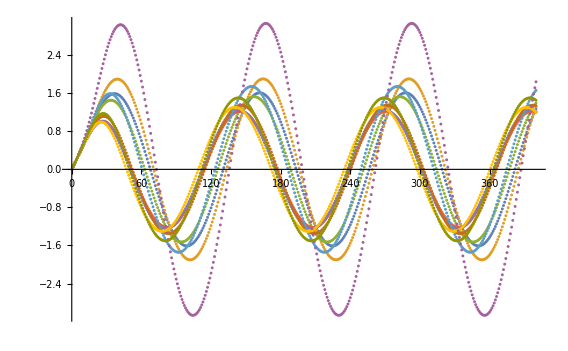

```mathematica
ListPlot[SolutionsCont]
```

```mathematica
SolutionsContMinusPhi0=Table[TruePhiSolverParamList[TrainingPoints[[i]],E0,0][[2]]-FL[xList,0],{i,1,Length[TrainingPoints]}];
```

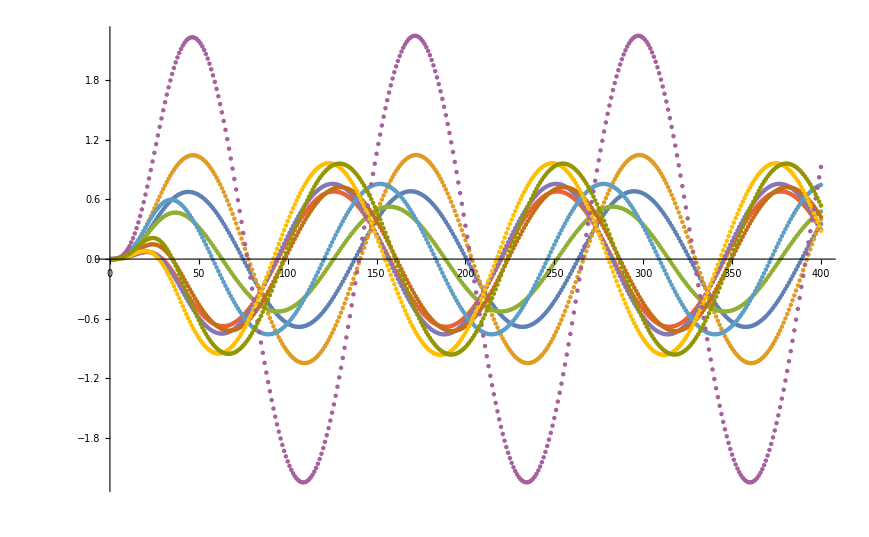

```mathematica
ListPlot[SolutionsContMinusPhi0]
```

```mathematica
NumberBasis=4;
```

```mathematica
SVDBasisGaler=Transpose[SingularValueDecomposition[SolutionsContMinusPhi0][[3]]][[1;;NumberBasis]];
```

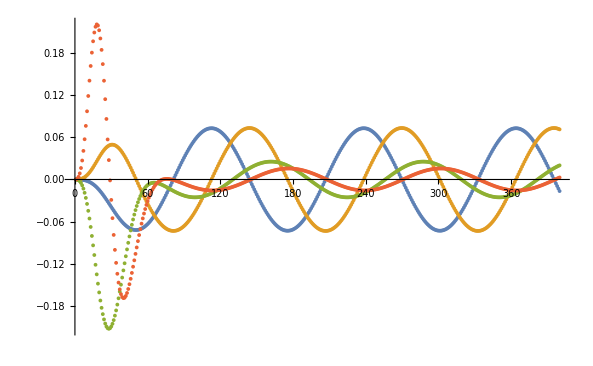

```mathematica
ListPlot[SVDBasisGaler]
```

```mathematica
PhiCoeffs=Array[PhiCoeffs0,NumberBasis];

PhiTrialFunc=FL[xList,0]+Table[Transpose[SVDBasisGaler[[1;;NumberBasis]]][[j]].PhiCoeffs,{j,1,Length[Transpose[SVDBasisGaler]]}];
```

## Step two: create the “questions” (Galerkin equations)

```mathematica
(*Eqs=-D2.Wf+(l*(l+1)/x^2+Vpot-1)*Wf;*)

-Graphics-;
```

```mathematica
ParamsTarget=Params0;
```

```mathematica
VParams[s_,ParamsList_,EE_]:=V[s,ParamsList[[1]],ParamsList[[2]],EE];
```

```mathematica
EqFixedGaler=(Eqs/.{D2->D2Mat,l->0,x->xList,Vpot->VParams[xList,{V01,V02},E0],Wf->PhiTrialFunc})[[3;;-3]];
```

```mathematica
EqFixedGaler[[10]]
```

33.3333 (0.479426-0.0020544 PhiCoeffs0[1]+0.00615079 PhiCoeffs0[2]-0.0347533 PhiCoeffs0[3]+0.0970452 PhiCoeffs0[4])-533.333 (0.522687-0.00272156 PhiCoeffs0[1]+0.00794612 PhiCoeffs0[2]-0.0445749 PhiCoeffs0[3]+0.118807 PhiCoeffs0[4])+1000. (0.564642-0.0035133 PhiCoeffs0[1]+0.00998225 PhiCoeffs0[2]-0.0555525 PhiCoeffs0[3]+0.140626 PhiCoeffs0[4])+(-1.+1/50 (0.641661 V01+0.870447 V02)) (0.564642-0.0035133 PhiCoeffs0[1]+0.00998225 PhiCoeffs0[2]-0.0555525 PhiCoeffs0[3]+0.140626 PhiCoeffs0[4])-533.333 (0.605186-0.00443688 PhiCoeffs0[1]+0.0122425 PhiCoeffs0[2]-0.0675384 PhiCoeffs0[3]+0.161518 PhiCoeffs0[4])+33.3333 (0.644218-0.00549812 PhiCoeffs0[1]+0.0147032 PhiCoeffs0[2]-0.0803448 PhiCoeffs0[3]+0.180499 PhiCoeffs0[4])

```mathematica
EqsGaler={};
For[ii=1,ii<=NumberBasis,ii++,

AppendTo[EqsGaler,  Expand[SVDBasisGaler[[ii]][[3;;-3]].EqFixedGaler]==0]

];
```

```mathematica
EqsGaler
```

{5.80978×10^-7-0.00144737 V01-0.00838953 V02-0.0237332 PhiCoeffs0[1]+0.0000386996 V01 PhiCoeffs0[1]+0.000446241 V02 PhiCoeffs0[1]-0.0627753 PhiCoeffs0[2]-0.0000567326 V01 PhiCoeffs0[2]-0.000309821 V02 PhiCoeffs0[2]-0.223428 PhiCoeffs0[3]+0.000263924 V01 PhiCoeffs0[3]+0.0014303 V02 PhiCoeffs0[3]+0.173793 PhiCoeffs0[4]-0.000183485 V01 PhiCoeffs0[4]+0.000229267 V02 PhiCoeffs0[4]==0,-7.61452×10^-7+0.00265159 V01+0.00977032 V02+0.0440531 PhiCoeffs0[1]-0.0000567326 V01 PhiCoeffs0[1]-0.000309821 V02 PhiCoeffs0[1]+0.0601564 PhiCoeffs0[2]+0.0000965224 V01 PhiCoeffs0[2]+0.000421505 V02 PhiCoeffs0[2]-0.248112 PhiCoeffs0[3]-0.000464376 V01 PhiCoeffs0[3]-0.00179927 V02 PhiCoeffs0[3]-0.230547 PhiCoeffs0[4]+0.000456493 V01 PhiCoeffs0[4]+0.000644762 V02 PhiCoeffs0[4]==0,7.25156×10^-8-0.0131149 V01-0.0444607 V02-0.200001 PhiCoeffs0[1]+0.000263924 V01 PhiCoeffs0[1]+0.0014303 V02 PhiCoeffs0[1]-0.219208 PhiCoeffs0[2]-0.000464376 V01 PhiCoeffs0[2]-0.00179927 V02 PhiCoeffs0[2]+0.634456 PhiCoeffs0[3]+0.00225579 V01 PhiCoeffs0[3]+0.0081621 V02 PhiCoeffs0[3]-0.417051 PhiCoeffs0[4]-0.00240215 V01 PhiCoeffs0[4]-0.00372441 V02 PhiCoeffs0[4]==0,-8.0404×10^-8+0.0166604 V01+0.022581 V02+0.172777 PhiCoeffs0[1]-0.000183485 V01 PhiCoeffs0[1]+0.000229267 V02 PhiCoeffs0[1]-0.207636 PhiCoeffs0[2]+0.000456493 V01 PhiCoeffs0[2]+0.000644762 V02 PhiCoeffs0[2]-0.411776 PhiCoeffs0[3]-0.00240215 V01 PhiCoeffs0[3]-0.00372441 V02 PhiCoeffs0[3]+4.51727 PhiCoeffs0[4]+0.00422658 V01 PhiCoeffs0[4]+0.00941512 V02 PhiCoeffs0[4]==0}

```mathematica
EqEnGaler[EE_]:=Module[{EqsEnGaler,EqsGalerIn,MatrixMIn,IndependentYIn},


EqsEnGaler=(Eqs/.{D2->D2Mat,l->0,x->xList,Vpot->VParams[xList,ParamsTarget,EE],Wf->PhiTrialFunc})[[3;;-3]];


EqsGalerIn={};
For[ii=1,ii<=NumberBasis,ii++,

AppendTo[EqsGalerIn,  Expand[SVDBasisGaler[[ii]][[3;;-3]].EqsEnGaler]==0]

];

MatrixMIn=Table[EqsGalerIn[[j]][[1]][[i]][[1]],{j,1,4},{i,2,5}];
IndependentYIn=Table[EqsGalerIn[[j]][[1]][[1]],{j,1,4}];

{MatrixMIn,IndependentYIn}


]
```

```mathematica
(*ResDets=Table[Det[EqEnGaler[i][[1]]],{i,1,100}]*)
```

{0.00209481,0.00219107,0.00232166,0.00245874,0.00258525,0.00269258,0.00277751,0.00283997,0.00288156,0.00290461,0.0029117,0.00290537,0.00288797,0.00286159,0.00282806,0.00278896,0.00274563,0.00269921,0.00265065,0.00260074,0.00255015,0.00249944,0.00244905,0.00239935,0.00235065,0.00230319,0.00225717,0.00221274,0.00217001,0.00212908,0.00209002,0.00205286,0.00201763,0.00198434,0.001953,0.00192359,0.00189609,0.00187049,0.00184675,0.00182482,0.00180469,0.0017863,0.0017696,0.00175456,0.00174113,0.00172926,0.0017189,0.00171,0.00170252,0.00169641,0.00169162,0.00168811,0.00168582,0.00168472,0.00168475,0.00168589,0.00168808,0.00169128,0.00169545,0.00170056,0.00170656,0.00171342,0.0017211,0.00172957,0.00173879,0.00174874,0.00175936,0.00177065,0.00178256,0.00179507,0.00180815,0.00182177,0.00183591,0.00185054,0.00186563,0.00188116,0.00189712,0.00191346,0.00193019,0.00194727,0.00196468,0.0019824,0.00200043,0.00201873,0.00203729,0.00205609,0.00207512,0.00209437,0.00211381,0.00213343,0.00215323,0.00217318,0.00219327,0.00221349,0.00223382,0.00225427,0.00227481,0.00229543,0.00231613,0.0023369}

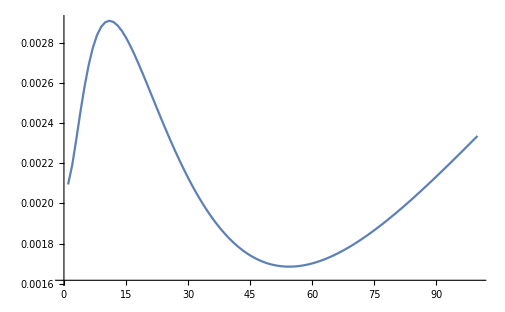

```mathematica
(*ListPlot[ResDets,Joined->True]*)
```

## Step 3 Solve the G equations for given params

```mathematica
EqsGalerParams=EqsGaler/.{V01->ParamsTarget[[1]],V02->ParamsTarget[[2]]};
```

```mathematica
EqsGalerParams
```

{0.481104-0.0569805 PhiCoeffs0[1]-0.0456648 PhiCoeffs0[2]-0.302017 PhiCoeffs0[3]+0.116038 PhiCoeffs0[4]==0,-0.367086+0.0611637 PhiCoeffs0[1]+0.0407456 PhiCoeffs0[2]-0.175723 PhiCoeffs0[3]-0.198469 PhiCoeffs0[4]==0,1.46075-0.27859 PhiCoeffs0[1]-0.14682 PhiCoeffs0[2]+0.335926 PhiCoeffs0[3]-0.555394 PhiCoeffs0[4]==0,1.25803+0.115022 PhiCoeffs0[1]-0.175559 PhiCoeffs0[2]-0.550119 PhiCoeffs0[3]+4.4978 PhiCoeffs0[4]==0}

```mathematica
SolGaler=FindRoot[EqsGalerParams,Transpose[{PhiCoeffs,ConstantArray[0,NumberBasis]}] ,PrecisionGoal->20,MaxIterations->500]
```

{PhiCoeffs0[1]→1.40923,PhiCoeffs0[2]→7.65274,PhiCoeffs0[3]→0.171522,PhiCoeffs0[4]→0.00394451}

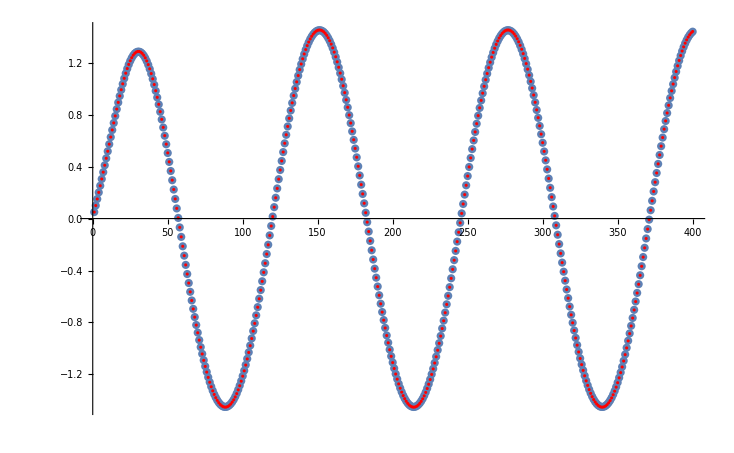

```mathematica
Show[ListPlot[{PhiTrialFunc/.SolGaler},PlotStyle->PointSize[0.008]],ListPlot[TruePhiSolverParamList[ParamsTarget,E0,0][[2]],PlotStyle->{Red,PointSize[0.003]}]]
```

```mathematica
GalerPhi0=PhiTrialFunc/.SolGaler;
```

```mathematica
TauKohnCorrection[phi_,alpha_,EE_]:=Module[{EqsIn,ResInt,iIn},

EqsIn=Eqs/.{D2->D2Mat,l->0,x->xList,Vpot->VParams[xList,alpha,EE],Wf->phi};
EqsIn=phi*EqsIn;

ResInt=0;

For[iIn=1,iIn<=len-4,iIn++,

ResInt=ResInt+EqsIn[[iIn]]*(3+(-1)^(iIn+1));


];

ResInt*dx/3*Sqrt[EE]*MuFactor

]
```

```mathematica
GalerPhaseShiftSolver[GalerList_,LL_]:=Module[{RL,YvalIn,YvalPIn},
YvalIn=GalerList[[n0]];
YvalPIn=(D1Mat.GalerList)[[n0]];
RL=1/X0*(YvalIn/YvalPIn);

Log[(HMinus[X0,LL]-X0*RL*HMinusPrime[X0,LL])/(HPlus[X0,LL]-X0*RL*HPlusPrime[X0,LL])]/(2*I)

]
```

```mathematica
GalerPhaseShiftSolver[GalerPhi0,0]
```

0.293882+0. ⅈ

```mathematica
TruePhiSolverParamList[ParamsTarget,E0,0][[1]]
```

0.293702+0. ⅈ

```mathematica
Expand[TauKohnCorrection[PhiTrialFunc,{V1,V2},E0]]
```

-7.75884×10^-7+0.004873 V1+0.0145091 V2+0.0638454 PhiCoeffs0[1]-0.000158985 V1 PhiCoeffs0[1]-0.000921517 V2 PhiCoeffs0[1]-0.00130345 PhiCoeffs0[1]^2+2.1254×10^-6 V1 PhiCoeffs0[1]^2+0.0000245078 V2 PhiCoeffs0[1]^2+0.048702 PhiCoeffs0[2]+0.000291266 V1 PhiCoeffs0[2]+0.00107319 V2 PhiCoeffs0[2]-0.00102817 PhiCoeffs0[1] PhiCoeffs0[2]-6.23157×10^-6 V1 PhiCoeffs0[1] PhiCoeffs0[2]-0.0000340311 V2 PhiCoeffs0[1] PhiCoeffs0[2]+0.00330371 PhiCoeffs0[2]^2+5.30106×10^-6 V1 PhiCoeffs0[2]^2+0.0000231493 V2 PhiCoeffs0[2]^2-0.00659487 PhiCoeffs0[3]-0.00144062 V1 PhiCoeffs0[3]-0.00488368 V2 PhiCoeffs0[3]-0.0232553 PhiCoeffs0[1] PhiCoeffs0[3]+0.0000289897 V1 PhiCoeffs0[1] PhiCoeffs0[3]+0.000157106 V2 PhiCoeffs0[1] PhiCoeffs0[3]-0.0256642 PhiCoeffs0[2] PhiCoeffs0[3]-0.0000510075 V1 PhiCoeffs0[2] PhiCoeffs0[3]-0.000197634 V2 PhiCoeffs0[2] PhiCoeffs0[3]+0.034841 PhiCoeffs0[3]^2+0.000123889 V1 PhiCoeffs0[3]^2+0.000448266 V2 PhiCoeffs0[3]^2-0.0141459 PhiCoeffs0[4]+0.00183027 V1 PhiCoeffs0[4]+0.00248059 V2 PhiCoeffs0[4]+0.0190351 PhiCoeffs0[1] PhiCoeffs0[4]-0.0000201542 V1 PhiCoeffs0[1] PhiCoeffs0[4]+0.0000251829 V2 PhiCoeffs0[1] PhiCoeffs0[4]-0.0240696 PhiCoeffs0[2] PhiCoeffs0[4]+0.0000501418 V1 PhiCoeffs0[2] PhiCoeffs0[4]+0.0000708214 V2 PhiCoeffs0[2] PhiCoeffs0[4]-0.0454938 PhiCoeffs0[3] PhiCoeffs0[4]-0.000263855 V1 PhiCoeffs0[3] PhiCoeffs0[4]-0.000409094 V2 PhiCoeffs0[3] PhiCoeffs0[4]+0.248045 PhiCoeffs0[4]^2+0.000232127 V1 PhiCoeffs0[4]^2+0.000517084 V2 PhiCoeffs0[4]^2

```mathematica
TruePhiSolverParamList[ParamsTarget,E0,0][[1]]
```

0.293702+0. ⅈ

```mathematica
TruePhiSolverParamList[ParamsTarget,E0,0][[1]]-GalerPhaseShiftSolver[GalerPhi0,0]
```

-0.000180064+0. ⅈ

```mathematica
AmpSolver[Yval_,PhaseShift_,LL_]:=Module[{},

Yval/(HMinus[X0,LL]-Exp[2*I*PhaseShift]*HPlus[X0,LL])/(2*I/(1+Exp[2*I*PhaseShift]))


]
```

```mathematica
ArcTan[
Tan[GalerPhaseShiftSolver[GalerPhi0,0]]-

TauKohnCorrection[GalerPhi0,ParamsTarget,E0]*
AmpSolver[GalerPhi0[[n0]],GalerPhaseShiftSolver[GalerPhi0,0],0]^2]
```

0.293699+0. ⅈ

```mathematica
TruePhiSolverParamList[ParamsTarget,E0,0][[1]]-ArcTan[
Tan[GalerPhaseShiftSolver[GalerPhi0,0]]-
TauKohnCorrection[GalerPhi0,ParamsTarget,E0]*
AmpSolver[GalerPhi0[[n0]],GalerPhaseShiftSolver[GalerPhi0,0],0]^2]
```

3.45545×10^-6+0. ⅈ

```mathematica
ResG=TauKohnCorrection[PhiTrialFunc,{V01,V02},E0]
```

0.0183068 (2 (1000. (0.909297-0.0622712 PhiCoeffs0[1]+0.0360564 PhiCoeffs0[2]-0.129393 PhiCoeffs0[3]-0.168852 PhiCoeffs0[4])+6+33.3333 (0.9463-0.0584261 PhiCoeffs0[1]+0.0410199 1-0.149688 PhiCoeffs0[3]-0.163112 PhiCoeffs0[4])) (0.909297-0.0622712 PhiCoeffs0[1]+0.0360564 PhiCoeffs0[2]-0.129393 PhiCoeffs0[3]-0.168852 PhiCoeffs0[4])+394+1)
 |  |  |  |

```mathematica
Expand[ResG]
```

-7.75884×10^-7+0.004873 V01+0.0145091 V02+0.0638454 PhiCoeffs0[1]-0.000158985 V01 PhiCoeffs0[1]-0.000921517 V02 PhiCoeffs0[1]-0.00130345 PhiCoeffs0[1]^2+2.1254×10^-6 V01 PhiCoeffs0[1]^2+0.0000245078 V02 PhiCoeffs0[1]^2+0.048702 PhiCoeffs0[2]+0.000291266 V01 PhiCoeffs0[2]+0.00107319 V02 PhiCoeffs0[2]-0.00102817 PhiCoeffs0[1] PhiCoeffs0[2]-6.23157×10^-6 V01 PhiCoeffs0[1] PhiCoeffs0[2]-0.0000340311 V02 PhiCoeffs0[1] PhiCoeffs0[2]+0.00330371 PhiCoeffs0[2]^2+5.30106×10^-6 V01 PhiCoeffs0[2]^2+0.0000231493 V02 PhiCoeffs0[2]^2-0.00659487 PhiCoeffs0[3]-0.00144062 V01 PhiCoeffs0[3]-0.00488368 V02 PhiCoeffs0[3]-0.0232553 PhiCoeffs0[1] PhiCoeffs0[3]+0.0000289897 V01 PhiCoeffs0[1] PhiCoeffs0[3]+0.000157106 V02 PhiCoeffs0[1] PhiCoeffs0[3]-0.0256642 PhiCoeffs0[2] PhiCoeffs0[3]-0.0000510075 V01 PhiCoeffs0[2] PhiCoeffs0[3]-0.000197634 V02 PhiCoeffs0[2] PhiCoeffs0[3]+0.034841 PhiCoeffs0[3]^2+0.000123889 V01 PhiCoeffs0[3]^2+0.000448266 V02 PhiCoeffs0[3]^2-0.0141459 PhiCoeffs0[4]+0.00183027 V01 PhiCoeffs0[4]+0.00248059 V02 PhiCoeffs0[4]+0.0190351 PhiCoeffs0[1] PhiCoeffs0[4]-0.0000201542 V01 PhiCoeffs0[1] PhiCoeffs0[4]+0.0000251829 V02 PhiCoeffs0[1] PhiCoeffs0[4]-0.0240696 PhiCoeffs0[2] PhiCoeffs0[4]+0.0000501418 V01 PhiCoeffs0[2] PhiCoeffs0[4]+0.0000708214 V02 PhiCoeffs0[2] PhiCoeffs0[4]-0.0454938 PhiCoeffs0[3] PhiCoeffs0[4]-0.000263855 V01 PhiCoeffs0[3] PhiCoeffs0[4]-0.000409094 V02 PhiCoeffs0[3] PhiCoeffs0[4]+0.248045 PhiCoeffs0[4]^2+0.000232127 V01 PhiCoeffs0[4]^2+0.000517084 V02 PhiCoeffs0[4]^2

```mathematica
Simplify[GalerPhaseShiftSolver[PhiTrialFunc,0]]
```

(0.-0.5 ⅈ) Log[((8.28213-10.9264 ⅈ)+(0.270206+0.962803 ⅈ) PhiCoeffs0[1]+(0.967202-0.269648 ⅈ) PhiCoeffs0[2]+(0.138996-0.319627 ⅈ) PhiCoeffs0[3]-(0.067124+0.203887 ⅈ) PhiCoeffs0[4])/((8.28213-10.9264 ⅈ)-(1.+0. ⅈ) PhiCoeffs0[1]-(0.00172563+1.00409 ⅈ) PhiCoeffs0[2]+(0.27018-0.220191 ⅈ) PhiCoeffs0[3]+(0.21444+0.00953567 ⅈ) PhiCoeffs0[4])]

```mathematica
EmulatedPhaseShift[EE_,Params_]:=Module[{EqInEm,EqsGalerIn,SolGalerIn,GalerPhi0In},

EqInEm=(Eqs/.{D2->D2Mat,l->0,x->xList,Vpot->VParams[xList,Params,EE],Wf->PhiTrialFunc})[[3;;-3]];

EqsGalerIn={};
For[ii=1,ii<=NumberBasis,ii++,

AppendTo[EqsGalerIn, SVDBasisGaler[[ii]][[3;;-3]].EqInEm==0]

];


SolGalerIn=FindRoot[EqsGalerIn,Transpose[{PhiCoeffs,ConstantArray[0,NumberBasis]}] ,PrecisionGoal->20,MaxIterations->500];


GalerPhi0In=PhiTrialFunc/.SolGalerIn;


ArcTan[
Tan[GalerPhaseShiftSolver[GalerPhi0In,0]]-0*TauKohnCorrection[GalerPhi0In,Params,EE]*
AmpSolver[GalerPhi0In[[n0]],GalerPhaseShiftSolver[GalerPhi0In,0],0]^2
]



]
```

```mathematica
EmulatedPhaseShift[E0,Params0];
```

```mathematica
TablePhase=Table[{i,180/Pi*EmulatedPhaseShift[i,Params0]},{i,1,100,5}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

{{1,6.01843+0. ⅈ},{6,54.23+0. ⅈ},{11,57.8365+0. ⅈ},{16,50.9292+0. ⅈ},{21,43.0896+0. ⅈ},{26,36.1053+0. ⅈ},{31,30.261+0. ⅈ},{36,25.4584+0. ⅈ},{41,21.521+0. ⅈ},{46,18.2831+0. ⅈ},{51,15.61+0. ⅈ},{56,13.3967+0. ⅈ},{61,11.5619+0. ⅈ},{66,10.0428+0. ⅈ},{71,8.78968+0. ⅈ},{76,7.76283+0. ⅈ},{81,6.92993+0. ⅈ},{86,6.26421+0. ⅈ},{91,5.74315+0. ⅈ},{96,5.34763+0. ⅈ}}

```mathematica
TablePhaseNoKohn=Table[EmulatedPhaseShift[i,Params0],{i,1,100,5}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{0.104073+0. ⅈ,0.945598+0. ⅈ,1.00901+0. ⅈ,0.888638+0. ⅈ,0.751912+0. ⅈ,0.630074+0. ⅈ,0.528111+0. ⅈ,0.444313+0. ⅈ,0.375606+0. ⅈ,0.319102+0. ⅈ,0.272452+0. ⅈ,0.233823+0. ⅈ,0.2018+0. ⅈ,0.175285+0. ⅈ,0.153412+0. ⅈ,0.135487-1.11022×10^-16 ⅈ,0.120947+0. ⅈ,0.109325+0. ⅈ,0.100227+0. ⅈ,0.0933199+0. ⅈ}

```mathematica
ResPhases=TablePhase
```

{{1,5.96296+0. ⅈ},{6,54.1788+0. ⅈ},{11,57.8122+0. ⅈ},{16,50.9152+0. ⅈ},{21,43.0814+0. ⅈ},{26,36.1006+0. ⅈ},{31,30.2585+0. ⅈ},{36,25.4573+0. ⅈ},{41,21.5206+0. ⅈ},{46,18.2832+0. ⅈ},{51,15.6104+0. ⅈ},{56,13.3971+0. ⅈ},{61,11.5623+0. ⅈ},{66,10.0431+0. ⅈ},{71,8.78984+0. ⅈ},{76,7.76285-6.36111×10^-15 ⅈ},{81,6.92977+0. ⅈ},{86,6.26384+0. ⅈ},{91,5.74258+0. ⅈ},{96,5.34684+0. ⅈ}}

```mathematica
SolExct=Table[180/Pi*TruePhiSolver[Params0[[1]],Params0[[2]],i,0][[1]],{i,1,100}]
```

{58.7411-6.36111×10^-15 ⅈ,59.3163+0. ⅈ,58.1365+0. ⅈ,56.5832+0. ⅈ,54.9537+0. ⅈ,53.3391+0. ⅈ,51.7714-6.36111×10^-15 ⅈ,50.2613+0. ⅈ,48.811+0. ⅈ,47.4195+0. ⅈ,46.0841+0. ⅈ,44.8016+0. ⅈ,43.5689+0. ⅈ,42.3828+0. ⅈ,41.2404+0. ⅈ,40.139+0. ⅈ,39.0761-6.36111×10^-15 ⅈ,38.0494+0. ⅈ,37.0568+0. ⅈ,36.0965+0. ⅈ,35.1667+0. ⅈ,34.2657+0. ⅈ,33.3921+0. ⅈ,32.5445+0. ⅈ,31.7217+0. ⅈ,30.9226+0. ⅈ,30.1459+0. ⅈ,29.3908+0. ⅈ,28.6564+0. ⅈ,27.9416-6.36111×10^-15 ⅈ,27.2458+0. ⅈ,26.5681+0. ⅈ,25.908+0. ⅈ,25.2645-6.36111×10^-15 ⅈ,24.6373+0. ⅈ,24.0256+0. ⅈ,23.4289+0. ⅈ,22.8466+0. ⅈ,22.2783+0. ⅈ,21.7235+0. ⅈ,21.1818+0. ⅈ,20.6526+0. ⅈ,20.1357+6.36111×10^-15 ⅈ,19.6305+0. ⅈ,19.1368+0. ⅈ,18.6542-6.36111×10^-15 ⅈ,18.1823-6.36111×10^-15 ⅈ,17.7208+0. ⅈ,17.2694+0. ⅈ,16.8279+0. ⅈ,16.3959+0. ⅈ,15.9732+0. ⅈ,15.5594+0. ⅈ,15.1544+0. ⅈ,14.7579+0. ⅈ,14.3697+0. ⅈ,13.9896+0. ⅈ,13.6173+0. ⅈ,13.2526+0. ⅈ,12.8953+0. ⅈ,12.5453+0. ⅈ,12.2024+0. ⅈ,11.8663+0. ⅈ,11.537+0. ⅈ,11.2141+0. ⅈ,10.8977+0. ⅈ,10.5875+0. ⅈ,10.2833+6.36111×10^-15 ⅈ,9.98506+0. ⅈ,9.6926+0. ⅈ,9.40579+0. ⅈ,9.12449+0. ⅈ,8.84857+0. ⅈ,8.57792+6.36111×10^-15 ⅈ,8.3124+0. ⅈ,8.0519+0. ⅈ,7.7963+0. ⅈ,7.5455+0. ⅈ,7.29939+0. ⅈ,7.05786+0. ⅈ,6.82082+0. ⅈ,6.58816+0. ⅈ,6.35978+0. ⅈ,6.13561-6.36111×10^-15 ⅈ,5.91553+0. ⅈ,5.69948+0. ⅈ,5.48735+0. ⅈ,5.27908+6.36111×10^-15 ⅈ,5.07457+0. ⅈ,4.87375+0. ⅈ,4.67654+0. ⅈ,4.48286+0. ⅈ,4.29265+0. ⅈ,4.10583+0. ⅈ,3.92234-6.36111×10^-15 ⅈ,3.7421+0. ⅈ,3.56505+0. ⅈ,3.39113-6.36111×10^-15 ⅈ,3.22028+0. ⅈ,3.05242+0. ⅈ}

```mathematica
ResPhases*180/Pi
```

```mathematica
FullEmulatorWithTrainingSingleEnergy[EE_,Params_,NumBasis_]:=Module[{EqInEm,EqsGalerIn,SolGalerIn,GalerPhi0In,NumberBasisIn,SolutionsContIn,
SolutionsContMinusPhi0In,SVDBasisGalerIn,PhiCoeffsIn,PhiTrialFuncIn


},

NumberBasisIn=NumBasis;
SolutionsContIn=Table[TruePhiSolverParamList[TrainingPoints[[i]],EE,0][[2]],{i,1,Length[TrainingPoints]}];
SolutionsContMinusPhi0In=Table[TruePhiSolverParamList[TrainingPoints[[i]],EE,0][[2]]-FL[xList,0],{i,1,Length[TrainingPoints]}];
SVDBasisGalerIn=Transpose[SingularValueDecomposition[SolutionsContMinusPhi0In][[3]]][[1;;NumberBasisIn]];
PhiCoeffsIn=Array[PhiCoeffs0,NumberBasisIn];

PhiTrialFuncIn=FL[xList,0]+Table[Transpose[SVDBasisGalerIn[[1;;NumberBasisIn]]][[j]].PhiCoeffsIn,{j,1,Length[Transpose[SVDBasisGalerIn]]}];



EqInEm=(Eqs/.{D2->D2Mat,l->0,x->xList,Vpot->VParams[xList,Params,EE],Wf->PhiTrialFuncIn})[[3;;-3]];

EqsGalerIn={};
For[ii=1,ii<=NumberBasisIn,ii++,

AppendTo[EqsGalerIn, SVDBasisGalerIn[[ii]][[3;;-3]].EqInEm==0]

];


SolGalerIn=FindRoot[EqsGalerIn,Transpose[{PhiCoeffsIn,ConstantArray[0,NumberBasisIn]}] ,PrecisionGoal->20,MaxIterations->500];


GalerPhi0In=PhiTrialFuncIn/.SolGalerIn;


ArcTan[
Tan[GalerPhaseShiftSolver[GalerPhi0In,0]]-0*TauKohnCorrection[GalerPhi0In,Params,EE]*
AmpSolver[GalerPhi0In[[n0]],GalerPhaseShiftSolver[GalerPhi0In,0],0]^2
]



]
```

```mathematica
FullEmulatorWithTrainingSingleEnergy[50,Params0,4]
```

0.293882+0. ⅈ

```mathematica
ResPhases=Table[{i,180/Pi*FullEmulatorWithTrainingSingleEnergy[i,Params0,4]},{i,1,100,0.333}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

{{1.,58.1181+0. ⅈ},{1.333,59.1645+0. ⅈ},{1.666,59.3934+0. ⅈ},{1.999,59.2782+6.36111×10^-15 ⅈ},{2.332,58.985+0. ⅈ},{2.665,58.5898+0. ⅈ},{2.998,58.1329+0. ⅈ},{3.331,57.6379+0. ⅈ},{3.664,57.1196+0. ⅈ},{3.997,56.5873+0. ⅈ},{4.33,56.0474+0. ⅈ},{4.663,55.5043+0. ⅈ},{4.996,54.961+0. ⅈ},{5.329,54.4197+0. ⅈ},{5.662,53.8819+0. ⅈ},{5.995,53.3486+0. ⅈ},{6.328,52.8206+0. ⅈ},{6.661,52.2985+0. ⅈ},{6.994,51.7825+0. ⅈ},{7.327,51.273+0. ⅈ},{7.66,50.77+0. ⅈ},{7.993,50.2737+0. ⅈ},{8.326,49.7841+0. ⅈ},{8.659,49.3011+0. ⅈ},{8.992,48.8246+0. ⅈ},{9.325,48.3547+0. ⅈ},{9.658,47.8913+0. ⅈ},{9.991,47.4341+0. ⅈ},{10.324,46.9832-6.36111×10^-15 ⅈ},{10.657,46.5384+0. ⅈ},{10.99,46.0996+0. ⅈ},{11.323,45.6667+0. ⅈ},{11.656,45.2395+0. ⅈ},{11.989,44.818+0. ⅈ},{12.322,44.402+0. ⅈ},{12.655,43.9914+0. ⅈ},{12.988,43.5861+0. ⅈ},{13.321,43.1859+0. ⅈ},{13.654,42.7909+0. ⅈ},{13.987,42.4007+0. ⅈ},{14.32,42.0154+0. ⅈ},{14.653,41.6349+0. ⅈ},{14.986,41.259+0. ⅈ},{15.319,40.8877+0. ⅈ},{15.652,40.5208+0. ⅈ},{15.985,40.1583+0. ⅈ},{16.318,39.8+0. ⅈ},{16.651,39.4459+0. ⅈ},{16.984,39.096+6.36111×10^-15 ⅈ},{17.317,38.75+0. ⅈ},{17.65,38.408+0. ⅈ},{17.983,38.0698+0. ⅈ},{18.316,37.7355+0. ⅈ},{18.649,37.4048+0. ⅈ},{18.982,37.0778+0. ⅈ},{19.315,36.7544+0. ⅈ},{19.648,36.4345+0. ⅈ},{19.981,36.118+0. ⅈ},{20.314,35.8049+0. ⅈ},{20.647,35.4952+0. ⅈ},{20.98,35.1887+0. ⅈ},{21.313,34.8854+6.36111×10^-15 ⅈ},{21.646,34.5852+0. ⅈ},{21.979,34.2881+0. ⅈ},{22.312,33.9941-6.36111×10^-15 ⅈ},{22.645,33.7031+0. ⅈ},{22.978,33.415-6.36111×10^-15 ⅈ},{23.311,33.1298-6.36111×10^-15 ⅈ},{23.644,32.8474+0. ⅈ},{23.977,32.5679+6.36111×10^-15 ⅈ},{24.31,32.291+0. ⅈ},{24.643,32.0169+0. ⅈ},{24.976,31.7455+0. ⅈ},{25.309,31.4767+0. ⅈ},{25.642,31.2104+0. ⅈ},{25.975,30.9467+0. ⅈ},{26.308,30.6855-6.36111×10^-15 ⅈ},{26.641,30.4268+0. ⅈ},{26.974,30.1705+0. ⅈ},{27.307,29.9166+0. ⅈ},{27.64,29.665+0. ⅈ},{27.973,29.4158+0. ⅈ},{28.306,29.1688+0. ⅈ},{28.639,28.9241+0. ⅈ},{28.972,28.6816+0. ⅈ},{29.305,28.4414+0. ⅈ},{29.638,28.2032+0. ⅈ},{29.971,27.9672+0. ⅈ},{30.304,27.7334+0. ⅈ},{30.637,27.5015+0. ⅈ},{30.97,27.2718+0. ⅈ},{31.303,27.044+0. ⅈ},{31.636,26.8182+0. ⅈ},{31.969,26.5944+0. ⅈ},{32.302,26.3726+0. ⅈ},{32.635,26.1526+0. ⅈ},{32.968,25.9346-6.36111×10^-15 ⅈ},{33.301,25.7184+0. ⅈ},{33.634,25.504-6.36111×10^-15 ⅈ},{33.967,25.2915+0. ⅈ},{34.3,25.0807+0. ⅈ},{34.633,24.8718+0. ⅈ},{34.966,24.6645+0. ⅈ},{35.299,24.459+0. ⅈ},{35.632,24.2552+0. ⅈ},{35.965,24.0531+0. ⅈ},{36.298,23.8527+0. ⅈ},{36.631,23.6539+0. ⅈ},{36.964,23.4567+0. ⅈ},{37.297,23.2612+0. ⅈ},{37.63,23.0672+0. ⅈ},{37.963,22.8748+0. ⅈ},{38.296,22.6839+0. ⅈ},{38.629,22.4946+0. ⅈ},{38.962,22.3068+0. ⅈ},{39.295,22.1205+0. ⅈ},{39.628,21.9357+0. ⅈ},{39.961,21.7523+0. ⅈ},{40.294,21.5704+0. ⅈ},{40.627,21.3899+0. ⅈ},{40.96,21.2108+0. ⅈ},{41.293,21.0332+0. ⅈ},{41.626,20.8569+0. ⅈ},{41.959,20.682+6.36111×10^-15 ⅈ},{42.292,20.5084+0. ⅈ},{42.625,20.3362+0. ⅈ},{42.958,20.1653+0. ⅈ},{43.291,19.9957+0. ⅈ},{43.624,19.8274+0. ⅈ},{43.957,19.6604+0. ⅈ},{44.29,19.4947+0. ⅈ},{44.623,19.3302+0. ⅈ},{44.956,19.167+0. ⅈ},{45.289,19.005+0. ⅈ},{45.622,18.8442-6.36111×10^-15 ⅈ},{45.955,18.6847+0. ⅈ},{46.288,18.5263+0. ⅈ},{46.621,18.3691+0. ⅈ},{46.954,18.2131+0. ⅈ},{47.287,18.0582+0. ⅈ},{47.62,17.9045+0. ⅈ},{47.953,17.7519+0. ⅈ},{48.286,17.6004+0. ⅈ},{48.619,17.4501+0. ⅈ},{48.952,17.3008+0. ⅈ},{49.285,17.1527+0. ⅈ},{49.618,17.0056+0. ⅈ},{49.951,16.8596+0. ⅈ},{50.284,16.7147+0. ⅈ},{50.617,16.5708+0. ⅈ},{50.95,16.4279+6.36111×10^-15 ⅈ},{51.283,16.2861+6.36111×10^-15 ⅈ},{51.616,16.1453+0. ⅈ},{51.949,16.0055+0. ⅈ},{52.282,15.8667+0. ⅈ},{52.615,15.7289+0. ⅈ},{52.948,15.592+0. ⅈ},{53.281,15.4562+0. ⅈ},{53.614,15.3213+0. ⅈ},{53.947,15.1874+0. ⅈ},{54.28,15.0544+0. ⅈ},{54.613,14.9223+0. ⅈ},{54.946,14.7912+0. ⅈ},{55.279,14.661-6.36111×10^-15 ⅈ},{55.612,14.5317+0. ⅈ},{55.945,14.4033+0. ⅈ},{56.278,14.2758+0. ⅈ},{56.611,14.1492+0. ⅈ},{56.944,14.0235+0. ⅈ},{57.277,13.8987+0. ⅈ},{57.61,13.7747+0. ⅈ},{57.943,13.6515+0. ⅈ},{58.276,13.5292+0. ⅈ},{58.609,13.4078+0. ⅈ},{58.942,13.2872+0. ⅈ},{59.275,13.1674+0. ⅈ},{59.608,13.0484-6.36111×10^-15 ⅈ},{59.941,12.9303-6.36111×10^-15 ⅈ},{60.274,12.8129+0. ⅈ},{60.607,12.6964-6.36111×10^-15 ⅈ},{60.94,12.5806+0. ⅈ},{61.273,12.4657+0. ⅈ},{61.606,12.3515+0. ⅈ},{61.939,12.2381+0. ⅈ},{62.272,12.1254+0. ⅈ},{62.605,12.0135+0. ⅈ},{62.938,11.9024+0. ⅈ},{63.271,11.792+0. ⅈ},{63.604,11.6823+0. ⅈ},{63.937,11.5734+0. ⅈ},{64.27,11.4652+0. ⅈ},{64.603,11.3577+0. ⅈ},{64.936,11.2509-6.36111×10^-15 ⅈ},{65.269,11.1449+0. ⅈ},{65.602,11.0395+0. ⅈ},{65.935,10.9349+0. ⅈ},{66.268,10.8309+0. ⅈ},{66.601,10.7276+0. ⅈ},{66.934,10.625+0. ⅈ},{67.267,10.5231+0. ⅈ},{67.6,10.4218+0. ⅈ},{67.933,10.3213+0. ⅈ},{68.266,10.2213-6.36111×10^-15 ⅈ},{68.599,10.1221+0. ⅈ},{68.932,10.0234+0. ⅈ},{69.265,9.92545+0. ⅈ},{69.598,9.8281+0. ⅈ},{69.931,9.73139+0. ⅈ},{70.264,9.63531+0. ⅈ},{70.597,9.53984+0. ⅈ},{70.93,9.445-6.36111×10^-15 ⅈ},{71.263,9.35077+0. ⅈ},{71.596,9.25715+0. ⅈ},{71.929,9.16413+0. ⅈ},{72.262,9.07171-6.36111×10^-15 ⅈ},{72.595,8.97989+0. ⅈ},{72.928,8.88865+0. ⅈ},{73.261,8.798+0. ⅈ},{73.594,8.70793+0. ⅈ},{73.927,8.61844+6.36111×10^-15 ⅈ},{74.26,8.52952+6.36111×10^-15 ⅈ},{74.593,8.44117-6.36111×10^-15 ⅈ},{74.926,8.35337+0. ⅈ},{75.259,8.26614+0. ⅈ},{75.592,8.17946+0. ⅈ},{75.925,8.09333+0. ⅈ},{76.258,8.00775+0. ⅈ},{76.591,7.92271+0. ⅈ},{76.924,7.83821+0. ⅈ},{77.257,7.75424+0. ⅈ},{77.59,7.6708+0. ⅈ},{77.923,7.58788+0. ⅈ},{78.256,7.50549+0. ⅈ},{78.589,7.42362+0. ⅈ},{78.922,7.34226+0. ⅈ},{79.255,7.26141+0. ⅈ},{79.588,7.18106+0. ⅈ},{79.921,7.10122+0. ⅈ},{80.254,7.02188+0. ⅈ},{80.587,6.94303+0. ⅈ},{80.92,6.86468+0. ⅈ},{81.253,6.78681+0. ⅈ},{81.586,6.70942+0. ⅈ},{81.919,6.63252+0. ⅈ},{82.252,6.5561+0. ⅈ},{82.585,6.48014+0. ⅈ},{82.918,6.40466+0. ⅈ},{83.251,6.32965+0. ⅈ},{83.584,6.2551+0. ⅈ},{83.917,6.18101+0. ⅈ},{84.25,6.10738+0. ⅈ},{84.583,6.0342+0. ⅈ},{84.916,5.96147+0. ⅈ},{85.249,5.88918+0. ⅈ},{85.582,5.81735+0. ⅈ},{85.915,5.74595+0. ⅈ},{86.248,5.67499+0. ⅈ},{86.581,5.60446+6.36111×10^-15 ⅈ},{86.914,5.53437+0. ⅈ},{87.247,5.4647+0. ⅈ},{87.58,5.39546+0. ⅈ},{87.913,5.32664+0. ⅈ},{88.246,5.25825-6.36111×10^-15 ⅈ},{88.579,5.19026+0. ⅈ},{88.912,5.12269+0. ⅈ},{89.245,5.05554+0. ⅈ},{89.578,4.98879+0. ⅈ},{89.911,4.92244+0. ⅈ},{90.244,4.8565+0. ⅈ},{90.577,4.79095+0. ⅈ},{90.91,4.7258+0. ⅈ},{91.243,4.66105+0. ⅈ},{91.576,4.59669+0. ⅈ},{91.909,4.53271+0. ⅈ},{92.242,4.46912+0. ⅈ},{92.575,4.40591+0. ⅈ},{92.908,4.34309+0. ⅈ},{93.241,4.28064+0. ⅈ},{93.574,4.21857+0. ⅈ},{93.907,4.15686+0. ⅈ},{94.24,4.09553-6.36111×10^-15 ⅈ},{94.573,4.03457+0. ⅈ},{94.906,3.97397+0. ⅈ},{95.239,3.91373+0. ⅈ},{95.572,3.85386+0. ⅈ},{95.905,3.79434+0. ⅈ},{96.238,3.73517+0. ⅈ},{96.571,3.67636+0. ⅈ},{96.904,3.6179+0. ⅈ},{97.237,3.55979+0. ⅈ},{97.57,3.50202+0. ⅈ},{97.903,3.4446+0. ⅈ},{98.236,3.38752+0. ⅈ},{98.569,3.33077+0. ⅈ},{98.902,3.27437+0. ⅈ},{99.235,3.21829+0. ⅈ},{99.568,3.16255+0. ⅈ},{99.901,3.10714+0. ⅈ}}

```mathematica
SolExct=Table[{i,180/Pi*TruePhiSolver[Params0[[1]],Params0[[2]],i,0][[1]]},{i,1,100,0.333}]
```

{{1.,58.7411-6.36111×10^-15 ⅈ},{1.333,59.3642+0. ⅈ},{1.666,59.475+0. ⅈ},{1.999,59.317+0. ⅈ},{2.332,59.0054+0. ⅈ},{2.665,58.6011+0. ⅈ},{2.998,58.1394+0. ⅈ},{3.331,57.6416+0. ⅈ},{3.664,57.1215+0. ⅈ},{3.997,56.5881+0. ⅈ},{4.33,56.0475+0. ⅈ},{4.663,55.5038+0. ⅈ},{4.996,54.9602-6.36111×10^-15 ⅈ},{5.329,54.4186+0. ⅈ},{5.662,53.8806-6.36111×10^-15 ⅈ},{5.995,53.3471+0. ⅈ},{6.328,52.819+0. ⅈ},{6.661,52.2967+0. ⅈ},{6.994,51.7807+0. ⅈ},{7.327,51.2711+0. ⅈ},{7.66,50.768+0. ⅈ},{7.993,50.2717+0. ⅈ},{8.326,49.7819+0. ⅈ},{8.659,49.2989+0. ⅈ},{8.992,48.8224+0. ⅈ},{9.325,48.3525+0. ⅈ},{9.658,47.889+0. ⅈ},{9.991,47.4318+0. ⅈ},{10.324,46.9808+0. ⅈ},{10.657,46.536+0. ⅈ},{10.99,46.0972+0. ⅈ},{11.323,45.6642-6.36111×10^-15 ⅈ},{11.656,45.237+0. ⅈ},{11.989,44.8154+0. ⅈ},{12.322,44.3994+0. ⅈ},{12.655,43.9887+0. ⅈ},{12.988,43.5834+0. ⅈ},{13.321,43.1832+0. ⅈ},{13.654,42.7881+0. ⅈ},{13.987,42.3979+0. ⅈ},{14.32,42.0126+0. ⅈ},{14.653,41.632+0. ⅈ},{14.986,41.2561+0. ⅈ},{15.319,40.8847+0. ⅈ},{15.652,40.5178+0. ⅈ},{15.985,40.1552+0. ⅈ},{16.318,39.7969+0. ⅈ},{16.651,39.4428+0. ⅈ},{16.984,39.0928+0. ⅈ},{17.317,38.7468+0. ⅈ},{17.65,38.4047+0. ⅈ},{17.983,38.0665+0. ⅈ},{18.316,37.7321+0. ⅈ},{18.649,37.4015+0. ⅈ},{18.982,37.0744+0. ⅈ},{19.315,36.7509+0. ⅈ},{19.648,36.431+0. ⅈ},{19.981,36.1145+0. ⅈ},{20.314,35.8013+0. ⅈ},{20.647,35.4915+0. ⅈ},{20.98,35.185+0. ⅈ},{21.313,34.8816-6.36111×10^-15 ⅈ},{21.646,34.5814+6.36111×10^-15 ⅈ},{21.979,34.2843+0. ⅈ},{22.312,33.9902+0. ⅈ},{22.645,33.6991+0. ⅈ},{22.978,33.411+0. ⅈ},{23.311,33.1257+0. ⅈ},{23.644,32.8433+0. ⅈ},{23.977,32.5637+0. ⅈ},{24.31,32.2869+0. ⅈ},{24.643,32.0127+0. ⅈ},{24.976,31.7412+0. ⅈ},{25.309,31.4723+0. ⅈ},{25.642,31.206+0. ⅈ},{25.975,30.9423+0. ⅈ},{26.308,30.681+0. ⅈ},{26.641,30.4222+0. ⅈ},{26.974,30.1658+0. ⅈ},{27.307,29.9119+0. ⅈ},{27.64,29.6602+0. ⅈ},{27.973,29.4109+0. ⅈ},{28.306,29.1639+0. ⅈ},{28.639,28.9192+6.36111×10^-15 ⅈ},{28.972,28.6766+0. ⅈ},{29.305,28.4363+0. ⅈ},{29.638,28.1981-6.36111×10^-15 ⅈ},{29.971,27.9621+6.36111×10^-15 ⅈ},{30.304,27.7281+0. ⅈ},{30.637,27.4962+0. ⅈ},{30.97,27.2664+0. ⅈ},{31.303,27.0386+0. ⅈ},{31.636,26.8128+0. ⅈ},{31.969,26.5889+0. ⅈ},{32.302,26.367+0. ⅈ},{32.635,26.1469+0. ⅈ},{32.968,25.9288+0. ⅈ},{33.301,25.7125+0. ⅈ},{33.634,25.4981+0. ⅈ},{33.967,25.2855+0. ⅈ},{34.3,25.0747+0. ⅈ},{34.633,24.8656+0. ⅈ},{34.966,24.6583+0. ⅈ},{35.299,24.4528+0. ⅈ},{35.632,24.2489+0. ⅈ},{35.965,24.0467-6.36111×10^-15 ⅈ},{36.298,23.8462+0. ⅈ},{36.631,23.6473+0. ⅈ},{36.964,23.4501+0. ⅈ},{37.297,23.2544+0. ⅈ},{37.63,23.0604+0. ⅈ},{37.963,22.8679+6.36111×10^-15 ⅈ},{38.296,22.677+0. ⅈ},{38.629,22.4876+0. ⅈ},{38.962,22.2997+0. ⅈ},{39.295,22.1133+0. ⅈ},{39.628,21.9284+0. ⅈ},{39.961,21.7449+0. ⅈ},{40.294,21.5629+0. ⅈ},{40.627,21.3824+0. ⅈ},{40.96,21.2032+6.36111×10^-15 ⅈ},{41.293,21.0254+0. ⅈ},{41.626,20.8491+0. ⅈ},{41.959,20.6741+0. ⅈ},{42.292,20.5004+0. ⅈ},{42.625,20.3281-6.36111×10^-15 ⅈ},{42.958,20.1571+6.36111×10^-15 ⅈ},{43.291,19.9875+0. ⅈ},{43.624,19.8191+0. ⅈ},{43.957,19.652+0. ⅈ},{44.29,19.4862+0. ⅈ},{44.623,19.3216+0. ⅈ},{44.956,19.1583+0. ⅈ},{45.289,18.9962+0. ⅈ},{45.622,18.8353+0. ⅈ},{45.955,18.6756+0. ⅈ},{46.288,18.5172+0. ⅈ},{46.621,18.3599+0. ⅈ},{46.954,18.2037+0. ⅈ},{47.287,18.0488+0. ⅈ},{47.62,17.8949+0. ⅈ},{47.953,17.7423+0. ⅈ},{48.286,17.5907+0. ⅈ},{48.619,17.4402+0. ⅈ},{48.952,17.2909+0. ⅈ},{49.285,17.1426+0. ⅈ},{49.618,16.9954+0. ⅈ},{49.951,16.8493+0. ⅈ},{50.284,16.7043+0. ⅈ},{50.617,16.5602+0. ⅈ},{50.95,16.4173-6.36111×10^-15 ⅈ},{51.283,16.2753+0. ⅈ},{51.616,16.1344+0. ⅈ},{51.949,15.9945-6.36111×10^-15 ⅈ},{52.282,15.8556+0. ⅈ},{52.615,15.7176+0. ⅈ},{52.948,15.5807+0. ⅈ},{53.281,15.4447+0. ⅈ},{53.614,15.3097+0. ⅈ},{53.947,15.1757+0. ⅈ},{54.28,15.0426+0. ⅈ},{54.613,14.9104+0. ⅈ},{54.946,14.7791+0. ⅈ},{55.279,14.6488+0. ⅈ},{55.612,14.5194+0. ⅈ},{55.945,14.3909+0. ⅈ},{56.278,14.2632+0. ⅈ},{56.611,14.1365+0. ⅈ},{56.944,14.0107+0. ⅈ},{57.277,13.8857+0. ⅈ},{57.61,13.7615+0. ⅈ},{57.943,13.6383+0. ⅈ},{58.276,13.5159+0. ⅈ},{58.609,13.3943-6.36111×10^-15 ⅈ},{58.942,13.2735+0. ⅈ},{59.275,13.1536+0. ⅈ},{59.608,13.0345+0. ⅈ},{59.941,12.9162+0. ⅈ},{60.274,12.7987+0. ⅈ},{60.607,12.682+0. ⅈ},{60.94,12.5661+0. ⅈ},{61.273,12.451+0. ⅈ},{61.606,12.3367+0. ⅈ},{61.939,12.2231+0. ⅈ},{62.272,12.1103+0. ⅈ},{62.605,11.9983+0. ⅈ},{62.938,11.887+0. ⅈ},{63.271,11.7764+0. ⅈ},{63.604,11.6666-6.36111×10^-15 ⅈ},{63.937,11.5575+0. ⅈ},{64.27,11.4492+0. ⅈ},{64.603,11.3415+0. ⅈ},{64.936,11.2346+0. ⅈ},{65.269,11.1284+0. ⅈ},{65.602,11.0229+6.36111×10^-15 ⅈ},{65.935,10.9181+0. ⅈ},{66.268,10.8139+0. ⅈ},{66.601,10.7105+0. ⅈ},{66.934,10.6077+0. ⅈ},{67.267,10.5057+0. ⅈ},{67.6,10.4042+0. ⅈ},{67.933,10.3035+0. ⅈ},{68.266,10.2034+0. ⅈ},{68.599,10.1039+0. ⅈ},{68.932,10.0052+0. ⅈ},{69.265,9.907+0. ⅈ},{69.598,9.80948+0. ⅈ},{69.931,9.7126+0. ⅈ},{70.264,9.61634+0. ⅈ},{70.597,9.5207+0. ⅈ},{70.93,9.42569+0. ⅈ},{71.263,9.33128+0. ⅈ},{71.596,9.23748+0. ⅈ},{71.929,9.14428+0. ⅈ},{72.262,9.05169+0. ⅈ},{72.595,8.95968+0. ⅈ},{72.928,8.86826+0. ⅈ},{73.261,8.77743+0. ⅈ},{73.594,8.68718+0. ⅈ},{73.927,8.5975+0. ⅈ},{74.26,8.50839+0. ⅈ},{74.593,8.41985+0. ⅈ},{74.926,8.33187+0. ⅈ},{75.259,8.24445+0. ⅈ},{75.592,8.15758+0. ⅈ},{75.925,8.07126+0. ⅈ},{76.258,7.98549+0. ⅈ},{76.591,7.90025+0. ⅈ},{76.924,7.81556+0. ⅈ},{77.257,7.73139+0. ⅈ},{77.59,7.64776+0. ⅈ},{77.923,7.56465+0. ⅈ},{78.256,7.48205+0. ⅈ},{78.589,7.39998+0. ⅈ},{78.922,7.31842+0. ⅈ},{79.255,7.23737+0. ⅈ},{79.588,7.15682+0. ⅈ},{79.921,7.07678+0. ⅈ},{80.254,6.99723+0. ⅈ},{80.587,6.91818+0. ⅈ},{80.92,6.83962-6.36111×10^-15 ⅈ},{81.253,6.76154+6.36111×10^-15 ⅈ},{81.586,6.68395+0. ⅈ},{81.919,6.60684+0. ⅈ},{82.252,6.53021+0. ⅈ},{82.585,6.45404+0. ⅈ},{82.918,6.37835+0. ⅈ},{83.251,6.30312+0. ⅈ},{83.584,6.22836+0. ⅈ},{83.917,6.15406+0. ⅈ},{84.25,6.08021+0. ⅈ},{84.583,6.00681+0. ⅈ},{84.916,5.93386+0. ⅈ},{85.249,5.86136+0. ⅈ},{85.582,5.78931+0. ⅈ},{85.915,5.71769+0. ⅈ},{86.248,5.64651+0. ⅈ},{86.581,5.57576+0. ⅈ},{86.914,5.50544+0. ⅈ},{87.247,5.43555+0. ⅈ},{87.58,5.36609+0. ⅈ},{87.913,5.29705+0. ⅈ},{88.246,5.22842-6.36111×10^-15 ⅈ},{88.579,5.16021+0. ⅈ},{88.912,5.09241+0. ⅈ},{89.245,5.02503+0. ⅈ},{89.578,4.95805+0. ⅈ},{89.911,4.89147+0. ⅈ},{90.244,4.8253+0. ⅈ},{90.577,4.75952+0. ⅈ},{90.91,4.69414+0. ⅈ},{91.243,4.62915+0. ⅈ},{91.576,4.56455+0. ⅈ},{91.909,4.50034+0. ⅈ},{92.242,4.43652+0. ⅈ},{92.575,4.37307+0. ⅈ},{92.908,4.31001+0. ⅈ},{93.241,4.24732+0. ⅈ},{93.574,4.18501+0. ⅈ},{93.907,4.12307+0. ⅈ},{94.24,4.0615-6.36111×10^-15 ⅈ},{94.573,4.00029+0. ⅈ},{94.906,3.93945+0. ⅈ},{95.239,3.87897+0. ⅈ},{95.572,3.81885+0. ⅈ},{95.905,3.75909+0. ⅈ},{96.238,3.69968+0. ⅈ},{96.571,3.64062+0. ⅈ},{96.904,3.58191+0. ⅈ},{97.237,3.52355+0. ⅈ},{97.57,3.46554+0. ⅈ},{97.903,3.40787+0. ⅈ},{98.236,3.35054+0. ⅈ},{98.569,3.29354+0. ⅈ},{98.902,3.23689+0. ⅈ},{99.235,3.18056+0. ⅈ},{99.568,3.12457+0. ⅈ},{99.901,3.06891+0. ⅈ}}

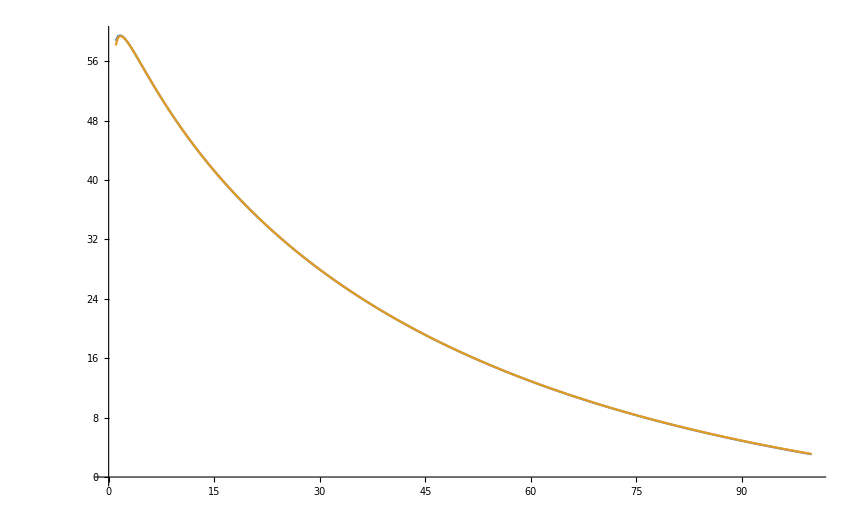

```mathematica
ListPlot[{SolExct,ResPhases},Joined->True]
```

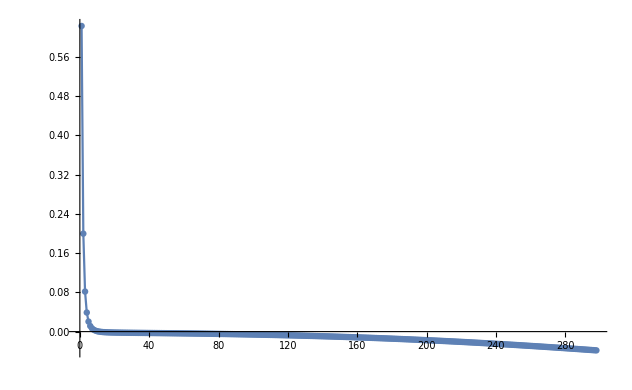

```mathematica
Show[ListPlot[{Transpose[SolExct][[2]]-Transpose[ResPhases][[2]]},Joined->True,PlotRange->All],ListPlot[{Transpose[SolExct][[2]]-Transpose[ResPhases][[2]]},Joined->False,PlotRange->All]]
```

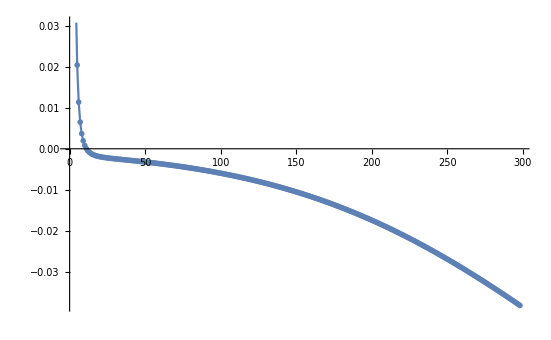

```mathematica
Show[ListPlot[{Transpose[SolExct][[2]]-Transpose[ResPhases][[2]]},Joined->True],ListPlot[{Transpose[SolExct][[2]]-Transpose[ResPhases][[2]]},Joined->False]]
```

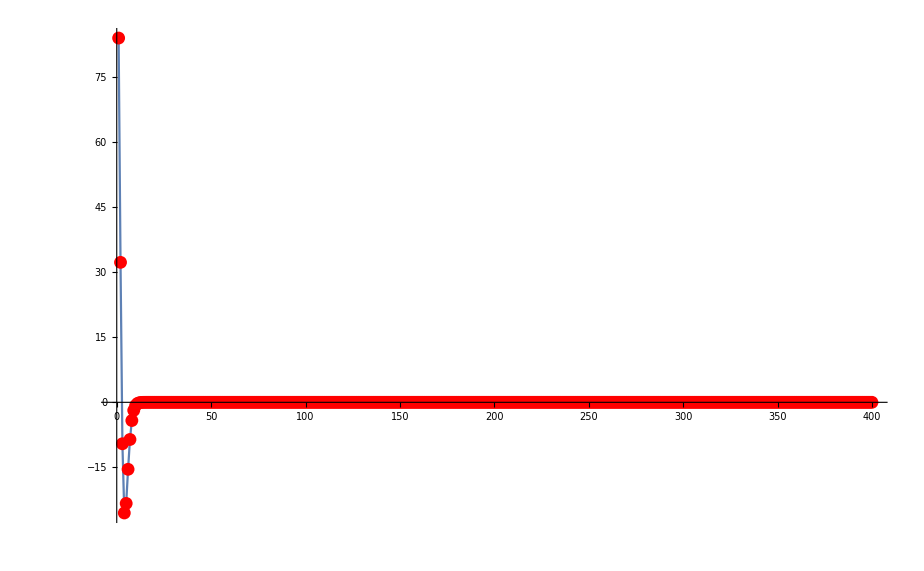

```mathematica
Show[ListPlot[VParams[xList,Params0,1],PlotRange->All,Joined->True],ListPlot[VParams[xList,Params0,1],PlotRange->All,Joined->False,PlotStyle->{Red,PointSize[0.01]}]]
```

## Applying the EIM

```mathematica
E0=50
```

50

```mathematica
VFull[r_,V0R_,V0S_,K1_,K2_,EE_]=(V0R*Exp[-K1*(r/(Sqrt[EE]*MuFactor))^2]+V0S*Exp[-K2*(r/(Sqrt[EE]*MuFactor))^2])1/EE
```

(ⅇ^(-(41.4421 K1 r^2)/EE) V0R+ⅇ^(-(41.4421 K2 r^2)/EE) V0S)/EE

```mathematica
RangeK1={1.487*0.5,1.487*1.5}
```

{0.7435,2.2305}

```mathematica
RangeK2={0.465*0.5,0.465*1.5}
```

{0.2325,0.6975}

```mathematica
SeedRandom[142857];
TrainingPointsK1=RandomReal[RangeK1,30]
```

{2.20406,1.72458,1.07826,1.15479,0.758713,1.31976,1.51313,0.927825,0.92687,1.79011,1.7075,0.918428,2.07139,0.743519,1.44479,2.13317,1.9181,1.44439,1.58698,2.03453,1.59582,1.94802,0.873024,1.5523,1.85957,0.971213,0.9915,1.89403,2.04199,1.69585}

```mathematica
SeedRandom[142857];
TrainingPointsK2=RandomReal[RangeK2,30]
```

{0.689233,0.539294,0.337182,0.361113,0.237257,0.412701,0.47317,0.29014,0.289842,0.559784,0.533951,0.287202,0.647746,0.232506,0.451801,0.667065,0.599811,0.451677,0.496265,0.636217,0.49903,0.609165,0.273003,0.48542,0.581507,0.303708,0.310052,0.592282,0.63855,0.530308}

```mathematica
SolutionsContK1=Table[VFull[xList,1,0,TrainingPointsK1[[i]],1,E0],{i,1,Length[TrainingPointsK1]}];
```

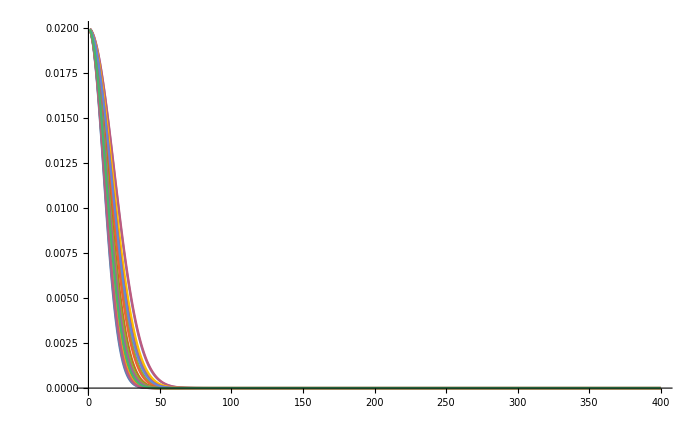

```mathematica
ListPlot[SolutionsContK1,Joined->True,PlotRange->All]
```

```mathematica
SolutionsContK2=Table[VFull[xList,0,1,1,TrainingPointsK2[[i]],E0],{i,1,Length[TrainingPointsK2]}];
```

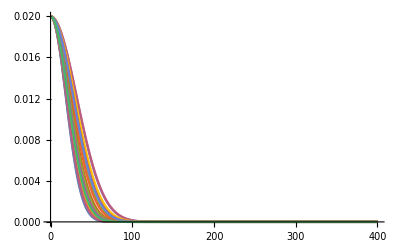

```mathematica
ListPlot[SolutionsContK2,Joined->True,PlotRange->All]
```

```mathematica
NumberBasisGaussians=3;
```

```mathematica
SVDBasisK1NotNorm=Transpose[SingularValueDecomposition[SolutionsContK1][[3]]][[1;;NumberBasisGaussians]];
```

```mathematica
SVDBasisK2NotNorm=Transpose[SingularValueDecomposition[SolutionsContK2][[3]]][[1;;NumberBasisGaussians]];
```

```mathematica
SVDBasisK1=Table[SVDBasisK1NotNorm[[i]]/SVDBasisK1NotNorm[[1]][[1]]*VFull[xList[[1]],1,0,TrainingPointsK1[[1]],1,E0],{i,1,Length[SVDBasisK1NotNorm]}];
```

```mathematica
SVDBasisK2=Table[SVDBasisK2NotNorm[[i]]/SVDBasisK2NotNorm[[1]][[1]]*VFull[xList[[1]],0,1,1,TrainingPointsK2[[1]],E0],{i,1,Length[SVDBasisK2NotNorm]}];
```

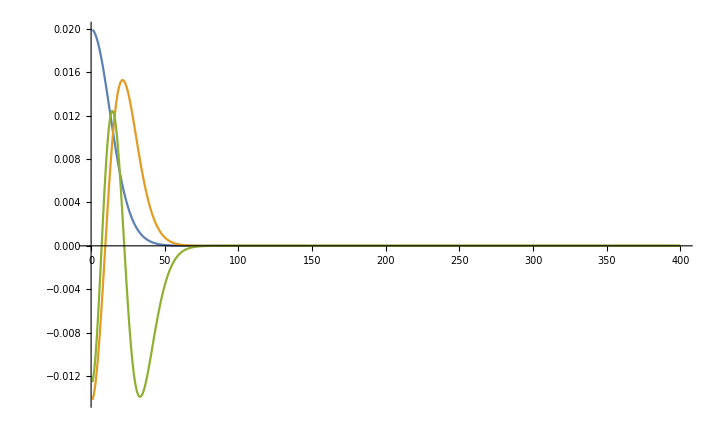

```mathematica
ListPlot[SVDBasisK1,Joined->True,PlotRange->All]
```

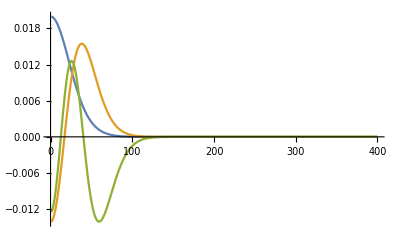

```mathematica
ListPlot[SVDBasisK2,Joined->True,PlotRange->All]
```

```mathematica
XMaxK1=Round[45/400*len]
XMaxK2=Round[80/400*len]
```

45

80

```mathematica
xK1=Reverse[Table[Round[XMaxK1/i],{i,1,NumberBasisGaussians}]]
```

{15,22,45}

```mathematica
xK2=Reverse[Table[Round[XMaxK2/i],{i,1,NumberBasisGaussians}]]
```

{27,40,80}

```mathematica
MK1=Table[SVDBasisK1[[i]][[xK1[[j]]]],{j,1,Length[xK1]},{i,1,Length[SVDBasisK1]}]
```

{{0.0103617,0.0105736,0.0123915},{0.00514017,0.0152468,0.00118088},{0.000181021,0.00174588,-0.00668873}}

```mathematica
MatrixForm[MK1]
```

(0.0103617 | 0.0105736 | 0.0123915
0.00514017 | 0.0152468 | 0.00118088
0.000181021 | 0.00174588 | -0.00668873)

```mathematica
MK2=Table[SVDBasisK2[[i]][[xK2[[j]]]],{j,1,Length[xK2]},{i,1,Length[SVDBasisK2]}]
```

{{0.0102827,0.0109301,0.0124783},{0.00492837,0.0153503,0.000253022},{0.000189197,0.0018298,-0.00693966}}

```mathematica
MK1Inv=Inverse[MK1];
MK2Inv=Inverse[MK2];
```

```mathematica
VK1Coeffs=Array[VK1Coeffs0,NumberBasisGaussians];
VK2Coeffs=Array[VK2Coeffs0,NumberBasisGaussians];
VK1Full=(Sum[VK1Coeffs[[i]]*SVDBasisK1[[i]],{i,1,Length[VK1Coeffs]}]);
VK2Full=(Sum[VK2Coeffs[[i]]*SVDBasisK2[[i]],{i,1,Length[VK2Coeffs]}]);
```

```mathematica
VK1Coeffs
```

{VK1Coeffs0[1],VK1Coeffs0[2],VK1Coeffs0[3]}

```mathematica
VFullParamsList=(V0R*VK1Full+V0S*VK2Full)
```

{V0R (0.0199089 VK1Coeffs0[1]-0.0141767 VK1Coeffs0[2]-0.0125562 VK1Coeffs0[3])+V0S (0.0199715 VK2Coeffs0[1]-0.0141105 VK2Coeffs0[2]-0.0124808 VK2Coeffs0[3]),398,V0R (6.85535×10^-111 VK1Coeffs0[1]+9.75951×10^-110 VK1Coeffs0[2]-1.03367×10^-108 VK1Coeffs0[3])+V0S (3.10417×10^-37 VK2Coeffs0[1]+4.42795×10^-36 VK2Coeffs0[2]-4.62808×10^-35 VK2Coeffs0[3])}
 |  |  |  |

```mathematica
CoeffSolverEIMK1[K1_]:=Module[{YvalsTrueIn,RulesValsIn,iIn},

YvalsTrueIn=VFull[Table[xList[[xK1[[jin]]]],{jin,1,Length[xK1]}],1,0,K1,1,E0];

RulesValsIn=MK1Inv.YvalsTrueIn;
Table[VK1Coeffs[[iIn]]->RulesValsIn[[iIn]],{iIn,1,Length[VK1Coeffs]}]

]
```

```mathematica
CoeffSolverEIMK1[1.4]
```

{VK1Coeffs0[1]→1.00685,VK1Coeffs0[2]→-0.0183664,VK1Coeffs0[3]→0.0140517}

```mathematica
CoeffSolverEIMK2[K2_]:=Module[{YvalsTrueIn,RulesValsIn},

YvalsTrueIn=VFull[Table[xList[[xK2[[jin]]]],{jin,1,Length[xK2]}],0,1,1,K2,E0];

RulesValsIn=MK2Inv.YvalsTrueIn;
Table[VK2Coeffs[[iIn]]->RulesValsIn[[iIn]],{iIn,1,Length[VK2Coeffs]}]


]
```

```mathematica
CoeffSolverEIMK2[0.6]
```

{VK2Coeffs0[1]→0.917299,VK2Coeffs0[2]→-0.116158,VK2Coeffs0[3]→-0.0066287}

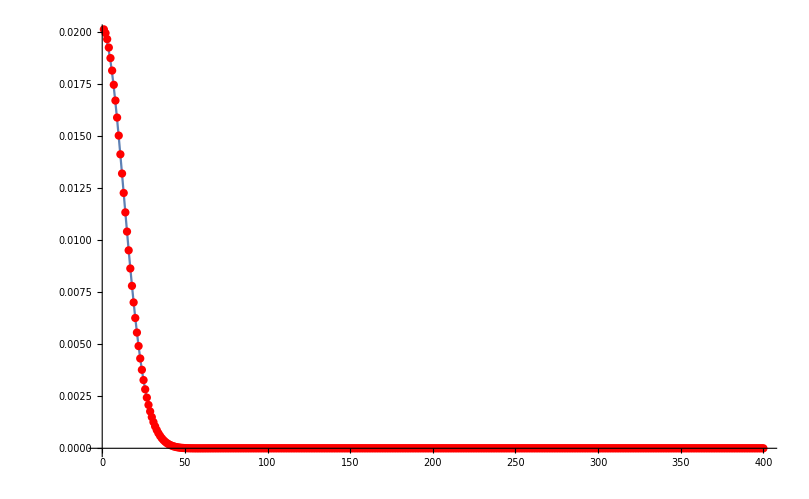

```mathematica
Show[ListPlot[VFull[xList,1,0,1.4,1,E0],Joined->True,PlotRange->All],ListPlot[VK1Full/.CoeffSolverEIMK1[1.4],PlotStyle->{Red}]]
```

```mathematica
CoeffSolverEIMK2[0.6]
```

{VK2Coeffs0[1]→0.917299,VK2Coeffs0[2]→-0.116158,VK2Coeffs0[3]→-0.0066287}

```mathematica
V1Range={ 100,300};
V2Range={-200,0};
```

```mathematica
SeedRandom[142857];
TrainingPointsEIM=Table[{RandomReal[V1Range],RandomReal[V2Range],RandomReal[RangeK1],RandomReal[RangeK2]},{i,1,50}]
```

{{296.444,-68.0455,1.07826,0.361113},{102.046,-122.494,1.51313,0.29014},{124.663,-59.2327,1.7075,0.287202},{278.6,-199.997,1.44479,0.667065},{257.983,-105.73,1.58698,0.636217},{214.636,-37.9936,0.873024,0.48542},{250.111,-169.373,0.9915,0.592282},{274.645,-71.9103,0.857657,0.667346},{126.366,-5.46784,1.85557,0.234202},{297.271,-69.5313,1.86882,0.274451},{134.448,-197.377,1.54321,0.505271},{229.145,-67.2429,1.61161,0.338524},{173.458,-38.2111,1.08444,0.440456},{211.247,-12.7556,0.890124,0.660662},{116.309,-18.5964,1.86307,0.280898},{294.726,-22.1221,1.65348,0.278481},{241.837,-159.35,1.78497,0.596666},{140.941,-36.949,1.16227,0.696463},{212.536,-22.4297,1.81313,0.511039},{136.042,-36.4472,2.01279,0.316166},{246.576,-159.134,1.2636,0.652919},{179.726,-121.986,1.61833,0.425903},{205.829,-133.317,1.18514,0.288505},{213.112,-117.325,1.9167,0.683917},{134.972,-34.5779,1.06209,0.62443},{152.617,-71.2573,1.42989,0.672645},{106.083,-132.133,1.33598,0.65673},{121.474,-58.2712,2.14534,0.372061},{261.065,-34.8394,2.1114,0.33002},{236.138,-2.84464,2.01728,0.663239},{248.932,-71.1281,1.35058,0.291566},{274.084,-98.4824,0.974264,0.335816},{289.229,-81.7694,1.83921,0.687651},{231.362,-76.9978,2.09496,0.425396},{238.206,-155.867,1.1244,0.303026},{253.399,-185.293,1.191,0.39058},{212.354,-57.6307,1.22584,0.449619},{253.616,-61.4908,1.84243,0.259447},{166.103,-114.938,0.775999,0.507799},{255.254,-144.413,1.56967,0.262959},{127.995,-63.4116,2.08016,0.661973},{179.215,-7.26611,1.63611,0.376073},{113.1,-123.809,0.999001,0.516372},{289.791,-92.5772,2.07466,0.463572},{290.025,-145.986,1.8087,0.579653},{248.418,-46.7568,1.29002,0.618694},{142.956,-104.962,2.08547,0.536973},{288.28,-159.164,1.84054,0.514778},{185.447,-149.306,2.05738,0.243877},{136.394,-34.3045,1.76358,0.364607}}

```mathematica
EqSolverFullParams[V0R_,V0S_,K1_,K2_,EE_,l_]:=PHI/.NDSolve[{-PHI''[XX]+(l*(l+1)/XX^2+VFull[XX,V0R,V0S,K1,K2,EE]-1)*PHI[XX]==0,PHI[epsilon]==epsilon^(l+1)/((2*l+1)!!),PHI'[epsilon]==(l+1)*epsilon^(l)/((2*l+1)!!)},PHI,{XX,epsilon,3*XMax},MaxStepSize->0.001][[1]][[1]](*Added the factor of 3 to XMax because otherwise with the change of variables the function had to extrapolate*)
```

```mathematica
TruePhiSolverFullParams[V0R_,V0S_,K1_,K2_,EE_,l_]:=Module[{Func,DelDel},

Func=EqSolverFullParams[V0R,V0S,K1,K2,EE,l];

DelDel=NormSolver[Func[X0],Func'[X0],l];
{DelDel,Table[Func[xList[[XXi]]],{XXi,1,Length[xList]}]}



]
```

```mathematica
SolutionsContEIM=Table[TruePhiSolverFullParams[TrainingPointsEIM[[i]][[1]],TrainingPointsEIM[[i]][[2]],TrainingPointsEIM[[i]][[3]],TrainingPointsEIM[[i]][[4]],E0,0][[2]],{i,1,Length[TrainingPointsEIM]}];
```

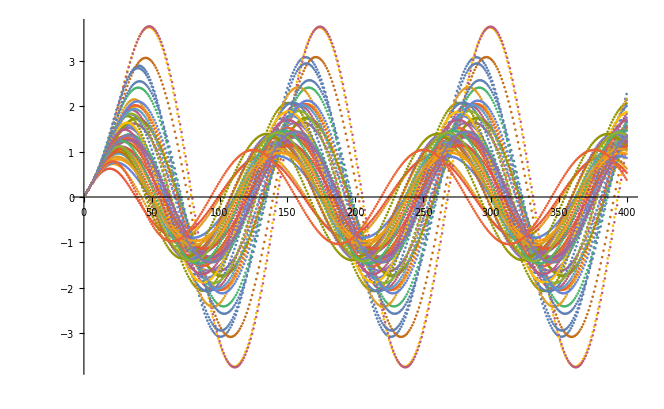

```mathematica
ListPlot[SolutionsContEIM]
```

```mathematica
SolutionsContMinusPhi0EIM=Table[TruePhiSolverFullParams[TrainingPointsEIM[[i]][[1]],TrainingPointsEIM[[i]][[2]],TrainingPointsEIM[[i]][[3]],TrainingPointsEIM[[i]][[4]],E0,0][[2]]-FL[xList,0],{i,1,Length[TrainingPointsEIM]}];
```

```mathematica
NumberBasisEIM=6;
```

```mathematica
SVDBasisGalerEIM=Transpose[SingularValueDecomposition[SolutionsContMinusPhi0EIM][[3]]][[1;;NumberBasisEIM]];
```

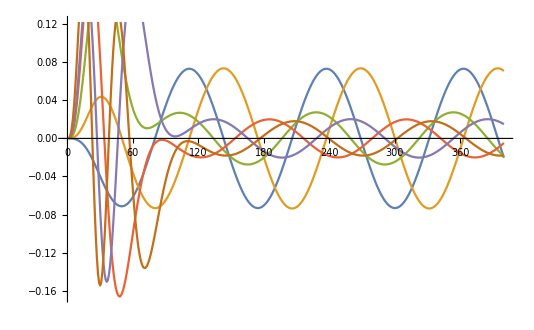

```mathematica
ListPlot[SVDBasisGalerEIM,Joined->True]
```

```mathematica
PhiCoeffsEIM=Array[PhiCoeffs0EIM,NumberBasisEIM];

PhiTrialFuncEIM=FL[xList,0]+Table[Transpose[SVDBasisGalerEIM[[1;;NumberBasisEIM]]][[j]].PhiCoeffsEIM,{j,1,Length[Transpose[SVDBasisGalerEIM]]}];
```

```mathematica
VFullParamsList
```

{V0R (0.0199089 VK1Coeffs0[1]-0.0141767 VK1Coeffs0[2]-0.0125562 VK1Coeffs0[3])+V0S (0.0199715 VK2Coeffs0[1]-0.0141105 VK2Coeffs0[2]-0.0124808 VK2Coeffs0[3]),398,V0R (6.85535×10^-111 VK1Coeffs0[1]+9.75951×10^-110 VK1Coeffs0[2]-1.03367×10^-108 VK1Coeffs0[3])+V0S (3.10417×10^-37 VK2Coeffs0[1]+4.42795×10^-36 VK2Coeffs0[2]-4.62808×10^-35 VK2Coeffs0[3])}
 |  |  |  |

```mathematica
EqFixedGalerEIM=(Eqs/.{D2->D2Mat,l->0,x->xList,Vpot->VFullParamsList,Wf->PhiTrialFuncEIM})[[3;;-3]];
```

```mathematica
EqFixedGalerEIM
```

{7+(0.149438-0.0000611 PhiCoeffs0EIM[1]+0.000160097 PhiCoeffs0EIM[2]+0.000799918 1+0.00181015 PhiCoeffs0EIM[4]+0.00231982 PhiCoeffs0EIM[5]+0.00494278 PhiCoeffs0EIM[6]) (1),394,-533.333 (0.841711-0.00957295 PhiCoeffs0EIM[1]+0.0729646 PhiCoeffs0EIM[2]-0.0153373 1-0.00769284 PhiCoeffs0EIM[4]+0.0167579 PhiCoeffs0EIM[5]-0.0180473 PhiCoeffs0EIM[6])+5+1}
 |  |  |  |

```mathematica
Params0EIM={Params0[[1]],Params0[[2]],1.4,0.5}
```

{200.,-91.85,1.4,0.5}

```mathematica
EqsGalerEIM={};
For[ii=1,ii<=NumberBasisEIM,ii++,

AppendTo[EqsGalerEIM,  Expand[SVDBasisGalerEIM[[ii]][[3;;-3]].EqFixedGalerEIM]==0]

];
```

```mathematica
EqsGalerEIMParamsFixed=EqsGalerEIM/.Join[{V0R->Params0EIM[[1]],V0S->Params0EIM[[2]]},CoeffSolverEIMK1[Params0EIM[[3]]],CoeffSolverEIMK2[Params0EIM[[4]]]]
```

{0.387544-0.0476397 PhiCoeffs0EIM[1]-0.0575563 PhiCoeffs0EIM[2]+0.247742 PhiCoeffs0EIM[3]+0.165893 PhiCoeffs0EIM[4]+0.0353936 PhiCoeffs0EIM[5]+0.0831115 PhiCoeffs0EIM[6]==0,-0.234273+0.0500839 PhiCoeffs0EIM[1]+0.0410728 PhiCoeffs0EIM[2]+0.211117 PhiCoeffs0EIM[3]-0.0898828 PhiCoeffs0EIM[4]-0.138656 PhiCoeffs0EIM[5]-0.14173 PhiCoeffs0EIM[6]==0,-1.13954+0.229842 PhiCoeffs0EIM[1]+0.175089 PhiCoeffs0EIM[2]-0.0185289 PhiCoeffs0EIM[3]+0.631719 PhiCoeffs0EIM[4]-0.835263 PhiCoeffs0EIM[5]-0.633902 PhiCoeffs0EIM[6]==0,0.503231+0.151209 PhiCoeffs0EIM[1]-0.0644603 PhiCoeffs0EIM[2]+0.622577 PhiCoeffs0EIM[3]+2.68717 PhiCoeffs0EIM[4]+1.89757 PhiCoeffs0EIM[5]-1.16603 PhiCoeffs0EIM[6]==0,1.04553+0.0618407 PhiCoeffs0EIM[1]-0.151806 PhiCoeffs0EIM[2]-0.824225 PhiCoeffs0EIM[3]+1.89312 PhiCoeffs0EIM[4]+4.83253 PhiCoeffs0EIM[5]+2.7243 PhiCoeffs0EIM[6]==0,1.14599+0.0568587 PhiCoeffs0EIM[1]-0.14457 PhiCoeffs0EIM[2]-0.642198 PhiCoeffs0EIM[3]-1.1594 PhiCoeffs0EIM[4]+2.72046 PhiCoeffs0EIM[5]+8.22613 PhiCoeffs0EIM[6]==0}

```mathematica
SolGalerEIM=FindRoot[EqsGalerEIMParamsFixed,Transpose[{PhiCoeffsEIM,ConstantArray[0,NumberBasisEIM]}] ,PrecisionGoal->20,MaxIterations->500]
```

{PhiCoeffs0EIM[1]→-0.766214,PhiCoeffs0EIM[2]→7.16407,PhiCoeffs0EIM[3]→-0.088449,PhiCoeffs0EIM[4]→0.0655163,PhiCoeffs0EIM[5]→-0.0233454,PhiCoeffs0EIM[6]→0.00193997}

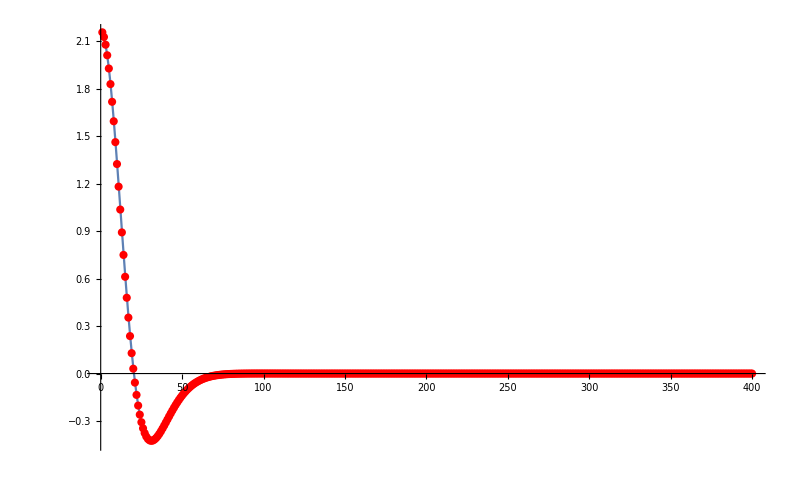

```mathematica
Show[ListPlot[VFull[xList,Params0EIM[[1]],Params0EIM[[2]],Params0EIM[[3]],Params0EIM[[4]],E0],Joined->True,PlotRange->All],ListPlot[VFullParamsList/.Join[{V0R->Params0EIM[[1]],V0S->Params0EIM[[2]]},CoeffSolverEIMK1[Params0EIM[[3]]],CoeffSolverEIMK2[Params0EIM[[4]]]],PlotStyle->{Red}]]
```

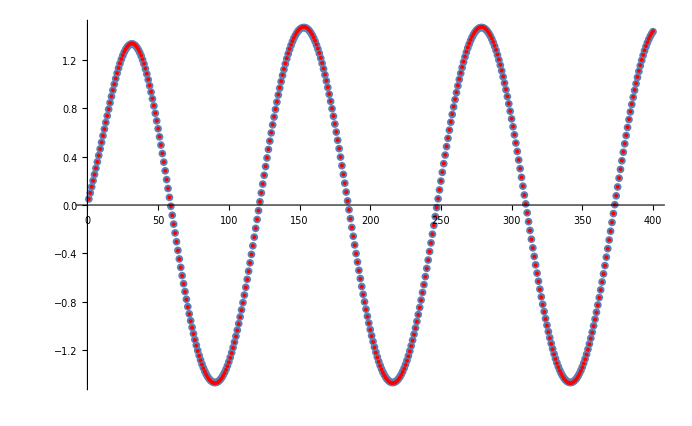

```mathematica
Show[ListPlot[{PhiTrialFuncEIM/.SolGalerEIM},PlotStyle->PointSize[0.008]],ListPlot[TruePhiSolverFullParams[Params0EIM[[1]],Params0EIM[[2]],Params0EIM[[3]],Params0EIM[[4]],E0,0][[2]],PlotStyle->{Red,PointSize[0.004]}]]
```